# 随机

## 随机变量的函数

## 成对散点图

```mathematica
irisData=ExampleData[{"Statistics","FisherIris"}];
```

```mathematica
groupData=SplitBy[irisData,Last]; (*列表分割*)
```

```mathematica
axeslabels=ExampleData[{"Statistics","FisherIris"},"ColumnHeadings"];
```

```mathematica
PairwiseListPlot[groupData,Headers->axeslabels]
```

-Graphics-

## 正交系投影

```mathematica
{sepalLength,sepalWidth,petalLength,petalWidth}=irisData[[All,#]]&/@Range@4;
```

```mathematica
covMatrix2=Covariance[Transpose@{sepalLength,sepalWidth}] (*花萼数据的协方差矩阵*)
```

{{0.685694,-0.042434},{-0.042434,0.189979}}

向正交系投影后的协方差矩阵

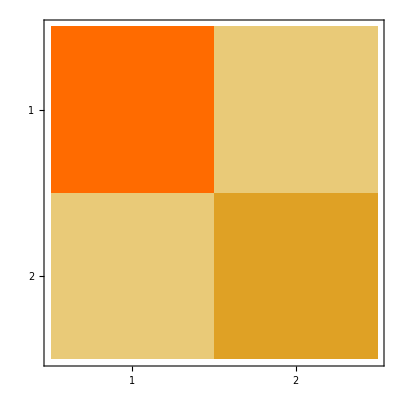
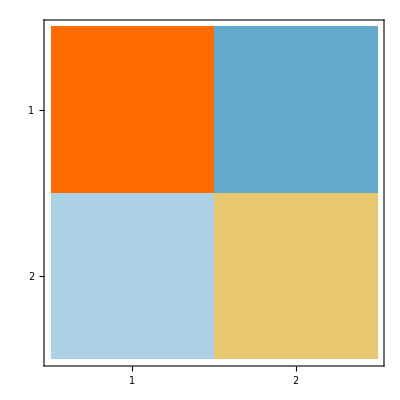
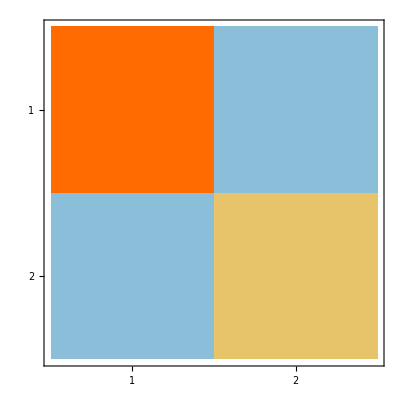
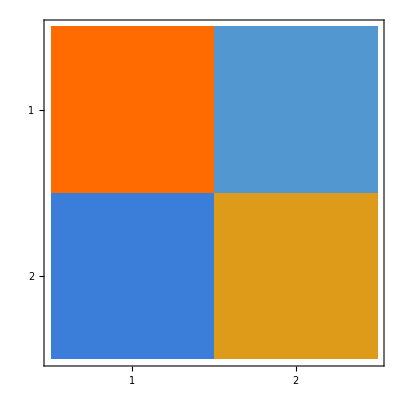
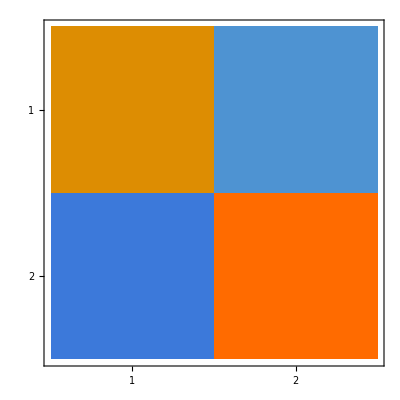
{{(0.598514 | 0.193433
0.193433 | 0.277159),-Graphics-},{(0.6893 | -0.0000660654
-0.0000660654 | 0.186373),-Graphics-},{(0.685694 | -0.042434
-0.042434 | 0.189979),-Graphics-},{(0.525016 | -0.235868
-0.235868 | 0.350657),-Graphics-},{(0.395402 | -0.247857
-0.247857 | 0.48027),-Graphics-}}

```mathematica
{MatrixForm@#,MatrixPlot@#}&@(Transpose@RotationMatrix[# Degree].covMatrix2.RotationMatrix[# Degree])&/@{-30,-4.85,0,30,45}
```

## 蒙特卡洛模拟

## 估算平方根

```mathematica
monteCarloSqrt2[n_]:=Count[RandomReal[{0,2},n],u_/;0<=u^2<=2]2/n//N
```

```mathematica
monteCarloSqrt2/@Table[10^i,{i,1,6}]
```

{1.4,1.52,1.388,1.4116,1.41788,1.41469}

## 估算积分

```mathematica
Integrate[x Sin[x]/2+8,{x,2,10}]
```

64+Cos[2]+1/2 (-10 Cos[10]-Sin[2]+Sin[10])

```mathematica
NIntegrate[x Sin[x]/2+8,{x,2,10},WorkingPrecision->10]
```

67.05255155

内置函数

```mathematica
NIntegrate[x Sin[x]/2+8,{x,2,10},Method->#]&/@{"MonteCarlo","QuasiMonteCarlo","AdaptiveMonteCarlo","AdaptiveQuasiMonteCarlo"}
```

{66.9068,66.996,66.573,67.0524}

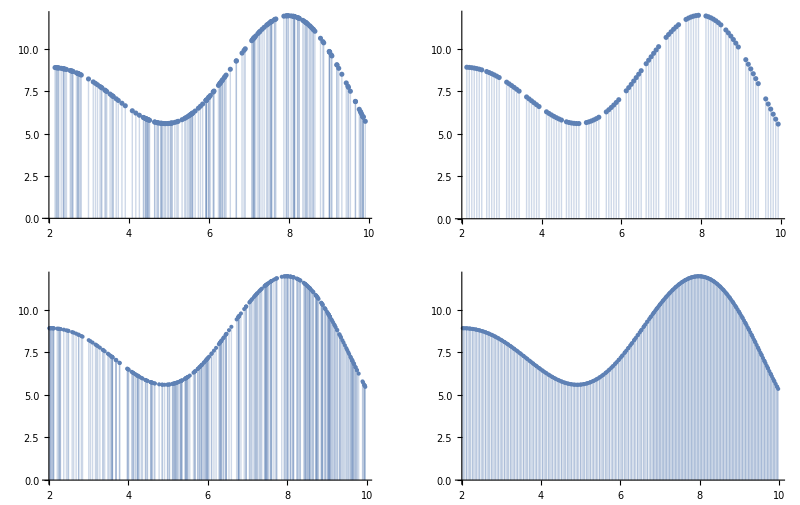

```mathematica
ListPlot[Last[Reap[NIntegrate[x Sin[x]/2+8,{x,2,10},Method->#,MaxPoints->100,EvaluationMonitor:>Sow[{x,x Sin[x]/2+8}]]]],Filling->0,AxesOrigin->{2,0}]&/@{"MonteCarlo","QuasiMonteCarlo","AdaptiveMonteCarlo","AdaptiveQuasiMonteCarlo"}//Quiet//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

代码实现

```mathematica
func1[x_]:=x Sin[x]/2+8
monteCarloInt[func_,n_]:=Count[Transpose@{RandomReal[{2,10},n],RandomReal[{0,12},n]},{u_,v_}/;v<=func[u]]96/n//N
```

```mathematica
monteCarloInt[func1,1000000]
```

67.0545

## 估算体积

```mathematica
Integrate[2-x^2-y^2,{x,-1,1},{y,-1,1}]
```

16/3

```mathematica
NIntegrate[2-x^2-y^2,{x,-1,1},{y,-1,1}]
```

5.33333

代码实现

```mathematica
(*定义函数*)
func2[x_,y_]:=2-x^2-y^2

(*蒙特卡罗积分函数*)
monteCarloInt2[func_,n_]:=Module[{count,points,volume},
points=Transpose@{RandomReal[{-1,1},n],RandomReal[{-1,1},n],RandomReal[{0,2},n]};
count=Count[points,{u_,v_,w_}/;w<=func[u,v]];
volume=8;
N[(count/n)*volume]]

(*调用函数*)
monteCarloInt2[func2,5000]
```

5.3088

## 估算圆周率

方法 1

```mathematica
monteCarloPi[n_]:=Module[{count,points,area},
points=Transpose@{RandomReal[{-1,1},n],RandomReal[{-1,1},n]};
count=Count[points,{u_,v_}/;u^2+v^2<=1];
area=4;
N[(count/n)*area]]
```

```mathematica
monteCarloPi[10^#]&/@Range@6
```

{2.4,3.16,3.044,3.1568,3.15908,3.14448}

方法 2：简化版布丰投针

```mathematica
monteCarloBuffonPi[l_,t_,n_]:=Module[{points,count,area},
points=Transpose@{RandomReal[{0,Pi/2},n],(*这里出现圆周率了？*)RandomReal[{0,t/2},n]};
count=Count[points,{u_,v_}/;v<=l Sin@u/2];
2l n/(t count)//N
]
```

```mathematica
monteCarloBuffonPi[1,2,10^#]&/@Range@6
```

{2.5,3.44828,3.09598,3.1211,3.15408,3.14209}

## 二项分布随机漫步

链接地址：https://reference.wolfram.com/language/ref/BinomialProcess.html.zh

```mathematica
(*定义函数来生成并展示随机路径和分布图*)binoPaths[probability_,stepNum_,pathNum_]:=Module[{data,sd,cf,sliced,pathPlot},(*生成二项过程数据*)data=RandomFunction[BinomialProcess[probability],{stepNum},pathNum];
(*提取特定步数的数据切片*)sd=data["SliceData",stepNum];
(*定义颜色函数*)cf=ColorData["Rainbow"];
(*生成结束位置的分布直方图*)sliced=BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{Min[sd],Max[sd]},{0,1}]),ImageSize->30]&[HistogramList[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/15]}]];
(*绘制路径*)pathPlot=ListLinePlot[data,ImageSize->400,PlotRange->All,AspectRatio->3/4,Epilog->Inset[sliced,{stepNum+0.5,Mean[sd]},{0,7.5}],PlotStyle->(cf/@Rescale[sd]),BaseStyle->Directive[Thin,Opacity[0.5]],PlotRangePadding->{{0,20},{0.5,7}}];
(*显示结果*)Show[pathPlot]]
```

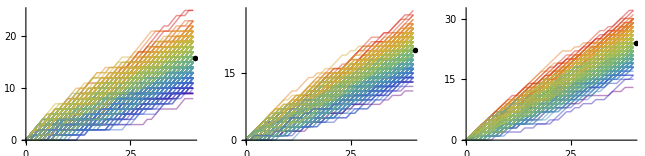

```mathematica
(*调用函数*)
binoPaths[#,40,500]&/@{0.4,0.5,0.6}//GraphicsRow
```

## 四元高斯随机数

```mathematica
meanVec=Mean/@{sepalLength,sepalWidth,petalLength,petalWidth}
```

{5.84333,3.05733,3.758,1.19933}

```mathematica
covMatrix4=Covariance@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}
```

{{0.685694,-0.042434,1.27432,0.516271},{-0.042434,0.189979,-0.329656,-0.121639},{1.27432,-0.329656,3.11628,1.29561},{0.516271,-0.121639,1.29561,0.581006}}

```mathematica
RandomVariate[MultinormalDistribution[meanVec,covMatrix4],200]//Show[PairwiseSmoothDensityHistogram[#,PlotTheme->"Minimal"],PairwiseListPlot[#,Headers->axeslabels,PlotTheme->"Minimal"]]&
```

-Graphics-